```mathematica
ABMInputs800=Import["/Users/thorsilver/Downloads/ABM outputs1/LPtau800runs_GEMSA_inputs.csv"];

ABMOutputs800=Import["/Users/thorsilver/Downloads/ABM outputs1/LPtau800runs GEMSA outputs only.csv"];
```

```mathematica
ABMOutputs800=Function[x,x/1000]/@ABMOutputs800;
ABMAssoc800 = AssociationThread[ABMInputs800 -> Flatten[ABMOutputs800]];
ABMnewData800=Dataset[ABMAssoc800];
ABMNormal800=Normal[ABMAssoc800];
ABMNormalRandom=RandomSample[ABMNormal800];
ABMtrain800=TakeDrop[ABMNormal800,640];
ABMtest800=ABMtrain800[[2]];
ABMtraining800=ABMtrain800[[1]];
trainDevSplit800=TakeDrop[ABMtraining800,512];
finalTrain800=trainDevSplit800[[1]];
finalDev800=trainDevSplit800[[2]];
finaltest800=ABMtest800;
```

```mathematica
Length[finalDev800]
Length[finalTrain800]
Length[finaltest800]
```

128

512

160

## NN Experiments

```mathematica
netSimple=NetChain[{10,BatchNormalizationLayer[],Tanh,15,15,15,15,15,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple=NetTrain[netSimple,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->500,Method->{"ADAM","L2Regularization"->0.05}]
```

NetChain[<>]

NetTrainResultsObject[<>]

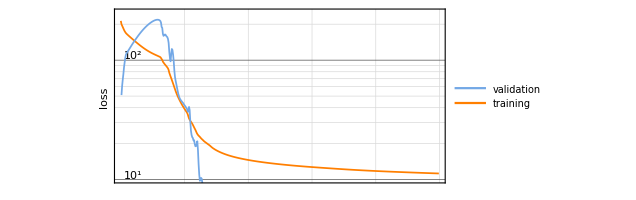

2.43338

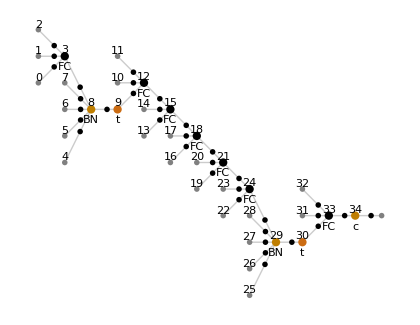

-Graphics-

```mathematica
trainedNetSimple["LossEvolutionPlot"]
trainedNetSimple["LowestValidationLoss"]
NetInformation[trainedNetSimple["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple["TrainedNet"],"SummaryGraphic"]
```

```mathematica
netSimple2=NetChain[{10,BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple2=NetTrain[netSimple2,finaltest800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->4000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

NetChain[<>]

NetTrainResultsObject[<>]

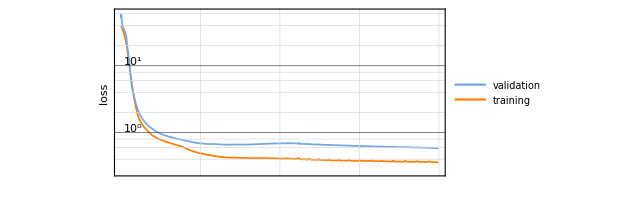

0.58319

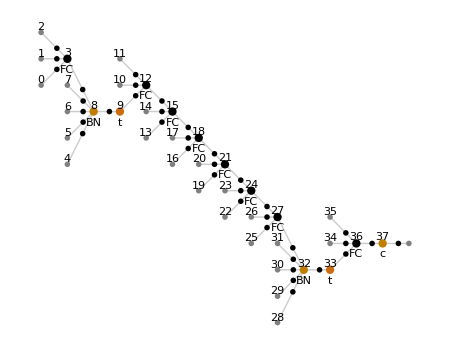

-Graphics-

```mathematica
trainedNetSimple2["LossEvolutionPlot"]
trainedNetSimple2["LowestValidationLoss"]
NetInformation[trainedNetSimple2["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple2["TrainedNet"],"SummaryGraphic"]
```

```mathematica
netSimple2=NetChain[{10,BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple2=NetTrain[netSimple2,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->4000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

NetChain[<>]

NetTrainResultsObject[<>]

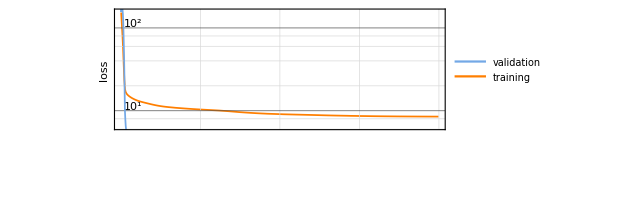

4.04817

-Graphics-

-Graphics-

```mathematica
trainedNetSimple2["LossEvolutionPlot"]
trainedNetSimple2["LowestValidationLoss"]
NetInformation[trainedNetSimple2["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple2["TrainedNet"],"SummaryGraphic"]
```

```mathematica
netSimple3=NetChain[{10,BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple3=NetTrain[netSimple3,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->1000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.05}]
```

NetChain[<>]

NetTrainResultsObject[<>]

```mathematica
trainedNetSimple3["LowestValidationLoss"]
```

2.88707

```mathematica
netSimple4=NetChain[{10,BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple4=NetTrain[netSimple4,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->1000,Method->{"ADAM","LearningRate"->0.0005, "L2Regularization"->0.04}]
```

NetChain[<>]

NetTrainResultsObject[<>]

```mathematica
trainedNetSimple4["LowestValidationLoss"]
```

3.42597

```mathematica
netSimple5=NetChain[{10,BatchNormalizationLayer[],Tanh,15,15,15,15,15,15,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple5=NetTrain[netSimple5,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->4000,Method->{"ADAM","LearningRate"->0.0005,"L2Regularization"->0.1}]
```

NetChain[<>]

NetTrainResultsObject[<>]

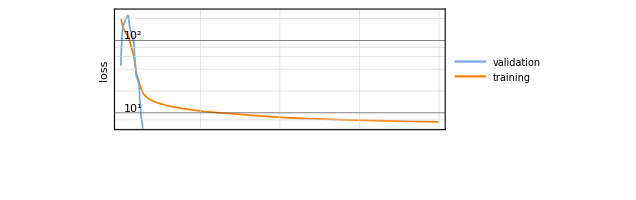

2.64168

-Graphics-

-Graphics-

```mathematica
trainedNetSimple5["LossEvolutionPlot"]
trainedNetSimple5["LowestValidationLoss"]
NetInformation[trainedNetSimple5["TrainedNet"],"MXNetNodeGraphPlot"]
NetInformation[trainedNetSimple5["TrainedNet"],"SummaryGraphic"]
```

```mathematica
netSimple6=NetChain[{10,BatchNormalizationLayer[],Tanh,15,15,15,15,15,15,15,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple6=NetTrain[netSimple6,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->4000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.035}]
```

NetChain[<>]

NetTrainResultsObject[<>]

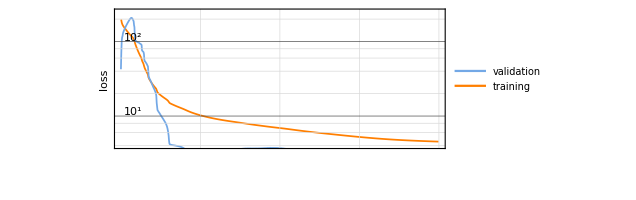

2.82514

```mathematica
trainedNetSimple6["LossEvolutionPlot"]
trainedNetSimple6["LowestValidationLoss"]
```

```mathematica
netSimple7=NetChain[{10,BatchNormalizationLayer[],Tanh,15,15,15,15,15,15,15,15,15,15,15,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple7=NetTrain[netSimple7,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"GPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

NetChain[<>]

NetTrainResultsObject[<>]

```mathematica
trainedNetSimple7["LowestValidationLoss"]
```

2.82401

NetChain[<>]

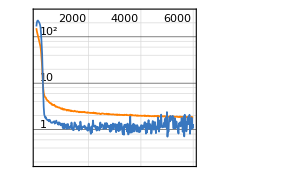
NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:1.0min  examples/s:49342
data | ,,  training examples:512  validation examples:160  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.82
validation | ,,  loss:5.12×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple8=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple8=NetTrain[netSimple8,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

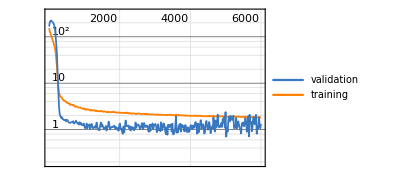
<|Loss→ | rounds
loss | -Graphics-|>

```mathematica
trainedNetSimple8["FinalPlots"]
```

```mathematica
trainedNetSimple8["RoundMeasurements"]
```

<|Loss→1.8232|>

```mathematica
best=trainedNetSimple8["BestValidationRound"]
trainedNetSimple8["ValidationLossList"][[best]]
```

5514

0.326605

NetChain[<>]

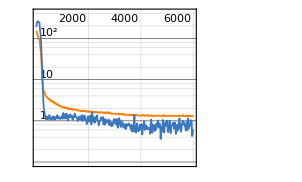
NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:1.1min  examples/s:48391
data | ,,  training examples:512  validation examples:128  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.27
validation | ,,  loss:1.96×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple9=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple9=NetTrain[netSimple9,finalTrain800,All,ValidationSet->finalDev800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

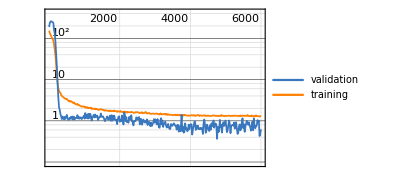
<|Loss→ | rounds
loss | -Graphics-|>

```mathematica
trainedNetSimple9["FinalPlots"]
```

```mathematica
trainedNetSimple9["RoundMeasurements"]
```

<|Loss→1.27217|>

```mathematica
best=trainedNetSimple9["BestValidationRound"]
trainedNetSimple9["ValidationLossList"][[best]]
```

5668

0.167929

NetChain[<>]

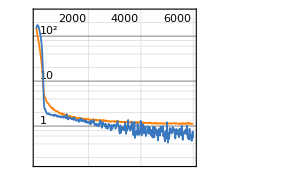
NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:59s  examples/s:52378
data | ,,  training examples:512  validation examples:160  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.09
validation | ,,  loss:2.72×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple10=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple10=NetTrain[netSimple10,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

```mathematica
trainedNetSimple10["FinalPlots"]
```

```mathematica
trainedNetSimple10["RoundMeasurements"]
```

```mathematica
best=trainedNetSimple10["BestValidationRound"]
trainedNetSimple10["ValidationLossList"][[best]]
```

5921

0.212548

```mathematica
netSimple11=NetChain[{BatchNormalizationLayer[],Tanh,50,50,50,50,50,50,50,50,50,50,50,BatchNormalizationLayer[],Tanh,1}]
trainedNetSimple11=NetTrain[netSimple11,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

NetChain[<>]

NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:1.1min  examples/s:47395
data | ,,  training examples:512  validation examples:160  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.82
validation | ,,  loss:5.12×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainedNetSimple11["FinalPlots"]
```

<|Loss→ | rounds
loss | -Graphics-|>

```mathematica
trainedNetSimple11["RoundMeasurements"]
trainedNetSimple11["TotalTrainingTime"]
```

<|Loss→1.8232|>

64.8175

```mathematica
best=trainedNetSimple11["BestValidationRound"]
trainedNetSimple11["ValidationLossList"][[best]]
```

5514

0.326605

NetChain[<>]

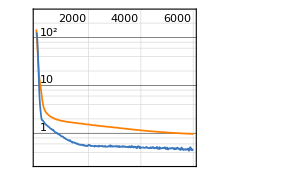
NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:37s  examples/s:83182
data | ,,  training examples:512  validation examples:128  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.62×10^-1
validation | ,,  loss:4.53×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple12=NetChain[{BatchNormalizationLayer[],Tanh,200,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple12=NetTrain[netSimple12,finalTrain800,All,ValidationSet->finalDev800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

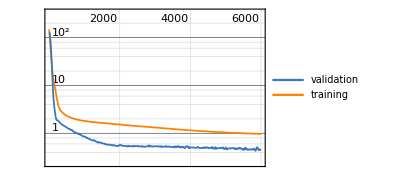
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→0.962342|>

5848

0.400727

```mathematica
trainedNetSimple12["FinalPlots"]
trainedNetSimple12["RoundMeasurements"]
best=trainedNetSimple12["BestValidationRound"]
trainedNetSimple12["ValidationLossList"][[best]]
```

NetChain[<>]

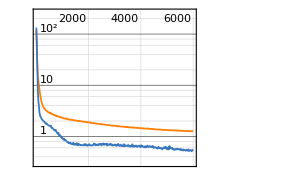
NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:60s  examples/s:51476
data | ,,  training examples:512  validation examples:128  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.25
validation | ,,  loss:4.87×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple13=NetChain[{BatchNormalizationLayer[],Tanh,500,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple13=NetTrain[netSimple13,finalTrain800,All,ValidationSet->finalDev800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

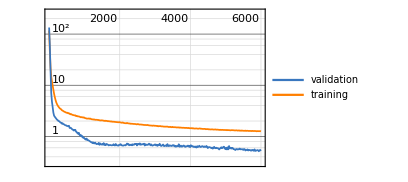
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.25461|>

5975

0.446038

```mathematica
trainedNetSimple13["FinalPlots"]
trainedNetSimple13["RoundMeasurements"]
best=trainedNetSimple13["BestValidationRound"]
trainedNetSimple13["ValidationLossList"][[best]]
```

NetChain[<>]

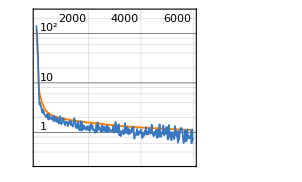
NetTrain Results
summary | ,,  batches:48000  rounds:6000  time:1.4min  examples/s:36833
data | ,,  training examples:512  validation examples:160  processed examples:3072000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.1
validation | ,,  loss:4.44×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple14=NetChain[{BatchNormalizationLayer[],Tanh,200,200,200,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple14=NetTrain[netSimple14,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"CPU",MaxTrainingRounds->6000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

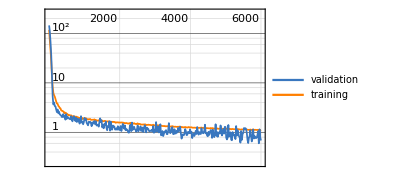
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→1.09988|>

83.403

5995

0.392537

```mathematica
trainedNetSimple14["FinalPlots"]
trainedNetSimple14["RoundMeasurements"]
trainedNetSimple14["TotalTrainingTime"]
best=trainedNetSimple14["BestValidationRound"]
trainedNetSimple14["ValidationLossList"][[best]]
```

NetChain[<>]

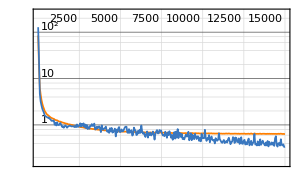
NetTrain Results
summary | ,,  batches:120000  rounds:15000  time:3.7min  examples/s:34444
data | ,,  training examples:512  validation examples:160  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:6.32×10^-1
validation | ,,  loss:2.78×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
netSimple15=NetChain[{BatchNormalizationLayer[],Tanh,200,200,200,BatchNormalizationLayer[],Tanh,1},"Input"->10,"Output"->"Scalar"]
trainedNetSimple15=NetTrain[netSimple15,finalTrain800,All,ValidationSet->finaltest800,TargetDevice->"CPU",MaxTrainingRounds->15000,Method->{"ADAM","LearningRate"->0.0003,"L2Regularization"->0.03}]
```

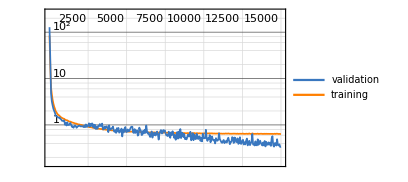
<|Loss→ | rounds
loss | -Graphics-|>

<|Loss→0.631878|>

222.969

13501

0.22382

```mathematica
trainedNetSimple15["FinalPlots"]
trainedNetSimple15["RoundMeasurements"]
trainedNetSimple15["TotalTrainingTime"]
best=trainedNetSimple15["BestValidationRound"]
trainedNetSimple15["ValidationLossList"][[best]]
```